# Lecture notes

```mathematica
φ[r_]:= Z^(3/2)/(√π) Exp[-Z r];
```

```mathematica
((- 1)/2 1/r^2 D[])/φ[r]
```

```mathematica
(Z^(3/2)/(√π) Exp[-Z r])^2+ (Z^(3/2)/(√π) Exp[-Z r])^2/.Z->2//FullSimplify
```

(16 ⅇ^(-4 r))/π

```mathematica
Integrate[4π r^2 (16 ⅇ^(-4 r))/π, {r, 0, ∞}]
```

2

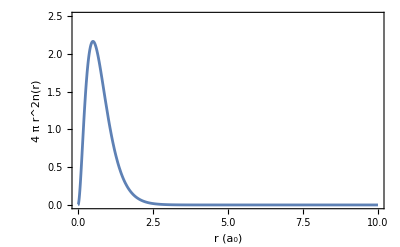

```mathematica
Plot[4π r^2 (16 ⅇ^(-4 r))/π, {r, 0, 10}, Frame ->True,PlotRange->{0,2.5},
FrameLabel->{"r (a_0)"," 4 π r^2n(r)"}]
```

```mathematica
eq = D[4π r^2 (16 ⅇ^(-4 r))/π,r ]==0
```

128 ⅇ^(-4 r) r-256 ⅇ^(-4 r) r^2==0

```mathematica
Solve[eq, r ]
```

{{r→0},{r→1/2}}